# Forecasting Regional Electrical Loads Using the Wolfram Language

Kyle MacLaury

Riccardo Di Virgilio

## Introduction

There are many applications of time series forecasting.  The utility industry, in particular, works with time series data from the meters and sensors distributed throughout their electrical networks.  This project explored the time series analysis and forecasting capabilities of the Wolfram Language using regional system load values published , and made available for download, by the New England Independent System Operator.

## System Load Data Import and Manipulation

Hourly total system load is publicly available for download from the New England Independent System Operator as CSV files.  Data from September 28, 2012 to June 8, 2019 was downloaded in fourteen day increments.  The CSV files have a number of header rows, and a trailer record, data records contain values for the date, hour, and total load.

### Import CSV File

```mathematica
Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\data\\rt_hourlysysload_20121011.csv"]
```

### Combine CSV Files

The CSV files were imported, and the data from the files combined into a single CSV (“alldata.csv”) file that could be re-imported for subsequent manipulations.

ClearAll[importData]

importData[] := importData @ FileNames["*.csv", FileNameJoin[{NotebookDirectory[], "data"}]]
importData[csv_List] := Join @@ Map[importData, csv]
importData[path_String] := Module[
	{csv, headers, data},
	csv = Import[path, "CSV"];
	headers = csv[[6]];
	data = csv[[7;;-2]];
	Transpose[AssociationThread[headers -> Transpose[data]], AllowedHeads→All]
]

exportPath = FileNameJoin[{NotebookDirectory[], "alldata.csv"}];
data = importData[];
Export[exportPath, Join[{Keys[First[data]]}, Values[data]], "CSV"]

### Creating a TimeSeries of Total System Load

The TimeSeries object within the Wolfram Language enables complex analyses to be performed on time series with a minimal amount of code.  The TimeSeries object can be created from lists of time ->value pairs.  The transformation to a TimeSeries object is simplest if the time values are expressed as Wolfram Language DateObjects.  The data provided by the New England Independent System Operator has the date and time values in separate columns, so the first step to the creation of a time series is to combine those columns into a single DateObject.

In addition, TimeSeries functions in the Wolfram Language work best when the data is evenly spaced, and there are no missing values.  The data available from New England ISO had a small number (approximately 12) of missing values.  To fill those in the SynthesizeMissingValues function was applied to a Dataset of the system load data.

### Synthesize Missing Values

```mathematica
loadDataComplete=SynthesizeMissingValues[SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Final Submission\\alldata.csv"]];
```

Dataset[<>]

### Creating DateObjects and TimeObjects

```mathematica
loadDateObjectTimeObject=loadDataComplete[All,{"Date"->DateObject,"HE"->TimeObject}];
```

### Creating a DateObject Column with Date and Hour

```mathematica
loadDataDateTime=loadDateObjectTimeObject[All,(Append[#,"DateTime"->DateObject[#Date,#HE]]&)];
```

### Creating a Time Series

neISOLoad=TimeSeries @ Map[
	{#["DateTime"], #["MWh"]} &,
	Normal[loadDataDateTime]
]

TimeSeries[…]

There are a handful of missing data points in this time series, so TimeSeriesResample is applied to it to achieve a TimeSeries of equal length to the Weather time series.

```mathematica
resampledNEISOLoad=TimeSeriesResample[neISOLoad,"Hour"]
```

TimeSeries[…]

### Acquiring Weather Data

Weather is a primary driver of the variability in electrical load.  Weather data for Boston was imported, and transformed into a TimeSeries object with the same dimensions of the System Load TimeSeries.  The weather data within the Wolfram Language is not regularly sampled, so the TimeSeriesRescale, and TimeSeriesResample functions are used to regularize the data into hourly intervals.

```mathematica
weatherData = TimeSeriesResample[
  TimeSeriesRescale[
   WeatherData["KBOS", "Temperature", {resampledNEISOLoad["FirstDate"], resampledNEISOLoad["LastDate"]}], 
   {resampledNEISOLoad["FirstDate"], resampledNEISOLoad["LastDate"]}
   ],
  "Hour"
  ]
```

TemporalData[TimeSeries, <<1>>]

### Synthesizing Missing Weather Data and Combining with Load Data

```mathematica
loadandWeatherData = SynthesizeMissingValues@Transpose@{
resampledNEISOLoad["Dates"], 
resampledNEISOLoad["Values"], 
Replace[weatherData["Values"], Except[_Real|_Integer] :> Missing["Temperature"], {1}]
};
```

### Combining Weather and System Load data, and creating a BusinessDay column

The BusinessDayQ function applies a calendar definition to DateObject values, and returns True if the day is a Business Day and False if it is not.  The default calendar was used.

```mathematica
combinedWeatherLoadBusinessDay = Dataset @ Apply[
<|
"Date" -> #1, 
"Temperature" -> #3,
"Hour"->TimeObject[#1],
"BusinessDay" -> BusinessDayQ[#1],
"Load" -> #2 
|>&,
loadandWeatherData,
{1}
];
```

$Aborted

## Transforming values for analysis

For the purpose of regression, the Date values need to be transformed to sequential integer values with 0 for the first value.  The Hour column needs to be translated to an integer as well, and the BusinessDay column needs to be translated to 0 or 1.  The following Functions do this transformation, paired with the native Boole function are applied to the dataset below.

### Combining System Load and Weather Data

```mathematica
timeObjecttoHourInteger[hour_TimeObject]:=DateValue[hour,"Hour"]
absoluteTimeDifferenceConverter[date_DateObject]:=QuantityMagnitude[DateDifference[DateObject[{2012,9,28,0}],date,"Hours"]]
```

```mathematica
datasetforregressionNOLAG=combinedWeatherLoadBusinessDay[All,{
"Hour"->timeObjecttoHourInteger,
"BusinessDay"->Boole,
"Date"->absoluteTimeDifferenceConverter}]
```

### Introducing Lags to System Load Data

A common technique for the analysis of time series data is to introduce lagged values into the dataset.  This allows statistical techniques to extract the relationship between a data point, and the points prior.  Thirty lagged values were created, and the lagged values combined into a dataset.

To accomplish this the load values are extracted into a list, and a table is constructed where each row represents the System Load data lagged 1 time step.  This creates lists that are longer than the original data set, by the number of lags introduced, so a function is applied to drop the first 30 time steps from the data.

```mathematica
loadList=Normal[datasetforregressionNOLAG[All,"Load"]];
```

```mathematica
shiftedLoadData=Table[PadLeft[Drop[loadList,-i],Length[loadList]],{i,30}]
```

```mathematica
{{{1}}, {{{, , , , }}}}
```

```mathematica
drop30[list_List]:=Drop[list,30]
```

```mathematica
droppedShiftedLoadData=Map[drop30,shiftedLoadData]
```

```mathematica
{{{1}}, {{{, , , , }}}}
```

```mathematica
listsofAssociation[lofA_List]:=Association[Range[1,30],lofA]
```

```mathematica
Transpose[Map[listsofAssociation,droppedShiftedLoadData,{2}]];
```

```mathematica
Grid[%42]
```

```mathematica
datasetofLaggedLoad=Dataset@Transpose[AssociationThread[Range[1,30]->droppedShiftedLoadData]];
```

## Statistical Analysis

## TimeSeriesForecast

The Wolfram Language has inbuilt fuctions for generating TimeSeriesModels, and using those models to generate TimeSeriesForecasts.  These functions evaluate multiple time series processes, and return the process with the highest explanatory value.  As we will see, this automatic evaluation of multiple models does not guarantee that the model returned is the best possible model to describe the data.

### TimeSeriesModelFit

```mathematica
loadTSModel=TimeSeriesModelFit[resampledNEISOLoad]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecast=TimeSeriesForecast[loadTSModel,{72}]
```

TemporalData[…]

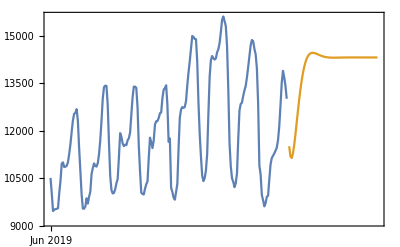

```mathematica
tsmodelDLP=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecast}]
```

#### TimeSeriesForecast specifying SARIMA with Automatic Options

```mathematica
tsmodelSARIMA=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMA=TimeSeriesForecast[tsmodelSARIMA,{72}]
```

TemporalData[…]

```mathematica
tsmodelDLPSARIMA=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMA}]
```

-Graphics-

#### TimeSeriesForecast specifying SARIMA with Specified Options

```mathematica
tsmodelSARIMASpecified=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{{1,1,1},{1,1,1},24}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMASpecified=TimeSeriesForecast[tsmodelSARIMASpecified,{72}]
```

TemporalData[…]

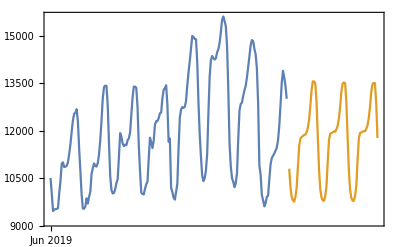

```mathematica
tsmodelDLPSARIMASpecified=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMASpecified}]
```

## Regression Analyses

### Data Import

The mldata file imported below contains values for 30 lagged time series of total system load, temperature values for each hour, an indicator of whether a time point falls on a business day, or not, and the time step.  The The columnHeads variable below illustrates the organization of the data.

```mathematica
mldata=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Final Submission\\mldata.wxf"];
```

```mathematica
columnHeads=v/@{"timeStep","temperature","BusinessDay","Lag1","Lag2","Lag3","Lag4","Lag5","Lag6","Lag7","Lag8","Lag9","Lag10","Lag11","Lag12","Lag13","Lag14","Lag15","Lag16","Lag17","Lag18","Lag19","Lag20","Lag21","Lag22","Lag23","Lag24","Lag25","Lag26","Lag27","Lag28","Lag29","Lag30","Load"};
```

### Linear Regression

A linear regression was performed using 30 lagged time series of the total system load. Also included was temperature data matched to load data, and a boolean variable for each time point that indicates if the time point falls on a business day or not.  The columnHeads variable in the cell above illustrates the organization of the data.

```mathematica
fit=LinearModelFit[mldata,Most@columnHeads,Most@columnHeads,NominalVariables->{v["BusinessDay"]}]
```

```mathematica
FittedModel[269.2410334546421-56.8971695357789 DiscreteIndicator[v["BusinessDay"],0,{0,1}]+1.0529628996334364 v["Lag1"]+0.03765016256540838 v["Lag10"]+«43»+0.3526658417437658 v["temperature"]-0.0004362725960037812 v["timeStep"]]
```

```mathematica
fit["AdjustedRSquared"]
```

0.982587

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 269.241 | 12.588 | 21.3886 | 4.15934×10^-101
v[timeStep] | -0.000436273 | 0.0000861454 | -5.06437 | 4.10985×10^-7
v[temperature] | 0.352666 | 0.144707 | 2.43711 | 0.0148083
v[BusinessDay][0] | -56.8972 | 3.32724 | -17.1004 | 2.12463×10^-65
v[Lag1] | 1.05296 | 0.00412572 | 255.219 | 0.
v[Lag2] | -0.0114452 | 0.0059939 | -1.90947 | 0.0562063
v[Lag3] | -0.0724189 | 0.00599093 | -12.0881 | 1.33883×10^-33
v[Lag4] | -0.0201555 | 0.00599798 | -3.36039 | 0.000778829
v[Lag5] | -0.0148526 | 0.0059439 | -2.4988 | 0.0124643
v[Lag6] | -0.00834035 | 0.00579861 | -1.43834 | 0.150344
v[Lag7] | 0.0152555 | 0.00567325 | 2.68902 | 0.00716832
v[Lag8] | -0.0244846 | 0.00561335 | -4.36186 | 0.0000129181
v[Lag9] | -0.010245 | 0.0056138 | -1.82497 | 0.0680106
v[Lag10] | 0.0376502 | 0.0056132 | 6.70743 | 1.99871×10^-11
v[Lag11] | 0.0150704 | 0.00561492 | 2.68399 | 0.00727686
v[Lag12] | -0.0410928 | 0.00561533 | -7.31797 | 2.54958×10^-13
v[Lag13] | 0.0307158 | 0.00561608 | 5.46926 | 4.53747×10^-8
v[Lag14] | 0.0200753 | 0.00561603 | 3.57465 | 0.000350976
v[Lag15] | -0.0581935 | 0.00561584 | -10.3624 | 3.86534×10^-25
v[Lag16] | -0.0234228 | 0.00561579 | -4.17088 | 0.0000303863
v[Lag17] | 0.0319223 | 0.00561599 | 5.68418 | 1.32065×10^-8
v[Lag18] | 0.0309066 | 0.00561609 | 5.50322 | 3.74476×10^-8
v[Lag19] | -0.00763677 | 0.005615 | -1.36007 | 0.173814
v[Lag20] | 0.00216162 | 0.00561476 | 0.384988 | 0.700248
v[Lag21] | -0.0274525 | 0.00561255 | -4.89127 | 1.00451×10^-6
v[Lag22] | 0.0191326 | 0.00561355 | 3.40829 | 0.000654162
v[Lag23] | 0.200296 | 0.00561341 | 35.6817 | 6.9929×10^-276
v[Lag24] | 0.289087 | 0.00567332 | 50.9556 | 0.
v[Lag25] | -0.316993 | 0.00579763 | -54.6764 | 0.
v[Lag26] | -0.196998 | 0.00594342 | -33.1455 | 1.07002×10^-238
v[Lag27] | 0.0212954 | 0.00599823 | 3.55028 | 0.000385124
v[Lag28] | 0.0454454 | 0.005992 | 7.58435 | 3.39058×10^-14
v[Lag29] | 0.0162445 | 0.00599447 | 2.70992 | 0.00673194
v[Lag30] | -0.0114218 | 0.00412937 | -2.76598 | 0.00567694

#### Linear Regression Results

The R squared value of 0.982587 illustrates that the model fits the data very well.  Weather and Business day each have significant, and apparently relatively large impacts on total system load.  Of additional interest is that the lagged values between 23 and 26 hours have P-values approaching zero, and also have relatively large estimate values.  This highlights what is apparent from visual inspection of total system load data, which is the fact that it has an apparent daily periodicity.

#### Non-Linear Regression

A non-linear regression was performed with a bias term, as well as amplitude and offset values for daily, weekly and yearly periods.

```mathematica
fit2=NonlinearModelFit[mldata⟦All,{1,-1}⟧,bias+ampDay Cos[offsetDay+(2π)/24 t]+ampWeek Cos[offsetWeek+(2π)/(7 24)t]+ampYear Cos[offsetYear+(2π)/(365 24)t],{bias,ampDay,offsetDay,ampWeek,offsetWeek,ampYear,offsetYear},{t}]
```

FittedModel[14333.6+450.155 Cos[«19»-«1»]+«1»+2039.02 Cos[27.1339+(π t)/12]]

```mathematica
fit2["AdjustedRSquared"]
```

0.979782

```mathematica
fit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
bias | 14333.6 | 8.55925 | 1674.64 | 0.
ampDay | 2039.02 | 12.0861 | 168.708 | 0.
offsetDay | 27.1339 | 0.0059272 | 4577.87 | 0.
ampWeek | 777.296 | 12.0846 | 64.3214 | 0.
offsetWeek | 1.35559 | 0.0155503 | 87.1742 | 0.
ampYear | 450.155 | 12.0976 | 37.2102 | 1.47289×10^-299
offsetYear | -12.4184 | 0.0268782 | -462.026 | 0.

#### Non-Linear Regression Results

All of the terms included in the model are highly significant with P-Values approaching zero.  In addition the Adjusted R Squared value of 0.979782 indicates that the model fits the data well.  An additional analysis that I would like to perform is to drop the weekly terms, and include the Business Day indicator.  I suspect that the weekly period is picking up on the lower load on non-business day weekends.  By dropping the weekly terms, and including the Business Day indicator the model should account for differences in load on holidays that fall on Monday through Friday.

## Machine Learning

## Data Preparation